```mathematica
results ={{{-0.31677346,-0.53264838, 0.3687124,-0.46297533},
{-0.71469407, 0.06729955,-0.85054426,-0.72343235},
{1.84593699, 0.27620355, 0.12258517,-0.46016522},
{2.82951901, 0.55065992,-0.25678624,-0.20574737},
{1.62816058,-0.12490481,-0.71879068,-0.38506339}},
{{-0.5,-0.33907784,-0.22011901,-0.5},
{-0.95,-0.45374554, 0.06273685,-0.30548588},
{-0.32478559, 0., 0., 0.},
{0., 0., 0., 0.},
{-0.5,-0.23065191,-0.24817284,-0.23598203}}}
```

{{{-0.316773,-0.532648,0.368712,-0.462975},{-0.714694,0.0672996,-0.850544,-0.723432},{1.84594,0.276204,0.122585,-0.460165},{2.82952,0.55066,-0.256786,-0.205747},{1.62816,-0.124905,-0.718791,-0.385063}},{{-0.5,-0.339078,-0.220119,-0.5},{-0.95,-0.453746,0.0627369,-0.305486},{-0.324786,0.,0.,0.},{0.,0.,0.,0.},{-0.5,-0.230652,-0.248173,-0.235982}}}

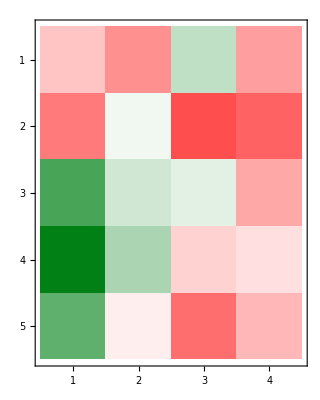

```mathematica
MatrixPlot[results[[1]], ColorFunction->"RedGreenSplit"]
```

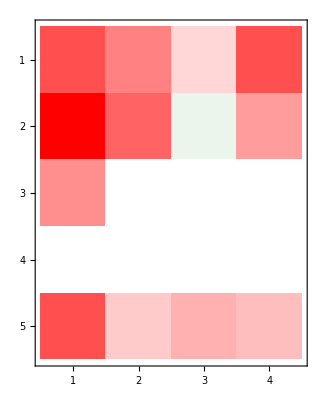

```mathematica
MatrixPlot[results[[2]], ColorFunction->"RedGreenSplit"]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/toddjohnson/Downloads/vscode-hello-python-master

```mathematica
Export["results-Qlearn.csv",Flatten[results, 1]]
```

results-Qlearn.csv

```mathematica
Flatten[results, 1]
```

{{-0.316773,-0.532648,0.368712,-0.462975},{-0.714694,0.0672996,-0.850544,-0.723432},{1.84594,0.276204,0.122585,-0.460165},{2.82952,0.55066,-0.256786,-0.205747},{1.62816,-0.124905,-0.718791,-0.385063},{-0.5,-0.339078,-0.220119,-0.5},{-0.95,-0.453746,0.0627369,-0.305486},{-0.324786,0.,0.,0.},{0.,0.,0.,0.},{-0.5,-0.230652,-0.248173,-0.235982}}

```mathematica
3.87-2.94
```

0.93

```mathematica
5.1-4.99
```

0.11

```mathematica
857.321+.95
```

858.271

```mathematica
1-.47
```

0.53

```mathematica
74.2-.57
```

73.63

```mathematica
9.56-7
```

2.56

```mathematica
.748+.145
```

0.893

```mathematica
6+5.02+7.004
```

18.024

```mathematica
18.8-10.53
```

8.27

```mathematica
12-3.987
```

8.013

```mathematica
18.8-10.53
```

8.27

```mathematica
0.765+3.876+5
```

9.641

```mathematica
6+.003+.9
```

6.903

```mathematica
67.89-67.65
```

0.24

```mathematica
Sqrt[5.]+3
```

5.23607

```mathematica
Sqrt[6.]+13
```

15.4495

```mathematica
Sqrt[10.]+13
```

16.1623

```mathematica
Sqrt[7.]+4
```

6.64575

```mathematica
Sqrt[6.]+5
```

7.44949

```mathematica
8+Sqrt[2.]
```

9.41421

```mathematica
Sqrt[8.]+2
```

4.82843

```mathematica
Sqrt[6.]
```

2.44949

```mathematica
3/2.
```

1.5

```mathematica
Sqrt[12.]
```

3.4641

```mathematica
Sqrt[12.]-1
```

2.4641

```mathematica
5/2.
```

2.5

```mathematica
1+π/2.
```

2.5708

```mathematica
4*Sqrt[2.]
```

5.65685

```mathematica
5^3
```

125

```mathematica
19/4.
```

4.75

```mathematica
r=Join[RandomInteger[5, 10], RandomInteger[10,10]]
```

{1,5,5,0,2,5,3,2,2,3,0,1,6,4,0,5,2,2,9,3}

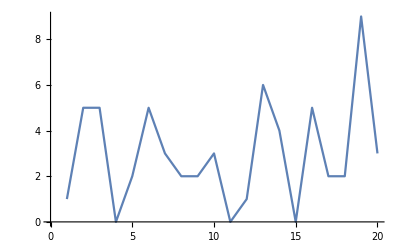

```mathematica
ListLinePlot[r]
```

```mathematica
Mean[r]
```

3

```mathematica
q =Accumulate[r]/Range[1, Length@r]
```

{1,3,11/3,11/4,13/5,3,3,23/8,25/9,14/5,28/11,29/12,35/13,39/14,13/5,11/4,46/17,8/3,3,3}

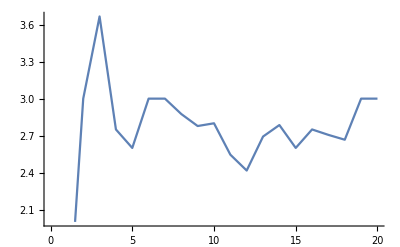

```mathematica
ListLinePlot[q]
```

```mathematica
QnInc[1,r_, α_]:= 0;
QnInc[n_, r_, α_]:=QnInc[n, r, α]= QnInc[n-1, r, α]+ α*(r[[n-1]] -QnInc[n-1, r, α])
```

```mathematica
QnInc[1, r]
```

0

```mathematica
QnInc[3,r, 0.1]
```

0.59

```mathematica
qtenth =Table[QnInc[i, r, 0.5], {i, 1, (Length@r)+1}]
```

{0,0.5,2.75,3.875,1.9375,1.96875,3.48438,3.24219,2.62109,2.31055,2.65527,1.32764,1.16382,3.58191,3.79095,1.89548,3.44774,2.72387,2.36193,5.68097,4.34048}

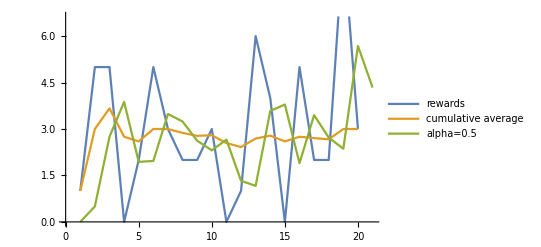

```mathematica
ListLinePlot[{r,q, qtenth}, PlotLegends-> {"rewards", "cumulative average", "alpha=0.5"}]
```

```mathematica
.1*(1-.1)^3*10
```

0.729

```mathematica
.1*10
```

1.

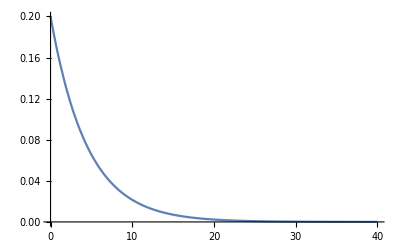

```mathematica
Plot[.2*(1-.2)^x, {x, 0, 40}, PlotRange->All]
```